# Εργασία 1η

## 1η Άσκηση

Ένα φορτισμένο σωματίδιο περνά διαδοχικά μέσα από N πανομοιότυπους, ανεξάρτητους ανιχνευτές που μετρούν τη θέση του με αποδοτικότητα (efficiency) 0.7 ο κάθε ένας. Για να ανακατασκευάσουμε την τροχιά του σωματιδίου χρειαζόμαστε τουλάχιστον 4 ανιχνεύσεις (“hits”).

Λύση

### 1ο ερώτημα: Πόση είναι η συνολική πιθανότητα ανίχνευσης του σωματιδίου αν N=6;

Η πιθανότητα ένα σωματίδιο να ανιχνευθεί από 4/6 ανιχνευτές, με efficiency 0.7 ο καθένας.

```mathematica
Probability[x ≥ 4, x \[Distributed] BinomialDistribution[6, 0.7]]
```

0.74431

### 2ο ερώτημα: Επιλέξτε τον ελάχιστο αριθμό ανιχνευτών ώστε να επιτύχουμε τουλάχιστον 99% πιθανότητα ανίχνευσης του σωματιδίου.

Ο ελάχιστος αριθμός ανιχνευτών για να έχουμε τουλάχιστον 99% πιθανότητα ανίχνευσης είναι:

```mathematica
Probability[x ≥ 4, x \[Distributed] BinomialDistribution[11, 0.7]]
```

0.995709

Στο παρακάτω διάγραμμα φαίνεται ότι με την αύξηση του n (ανιχνευτών), η πιθανότητα προσεγγίζει τη μονάδα.

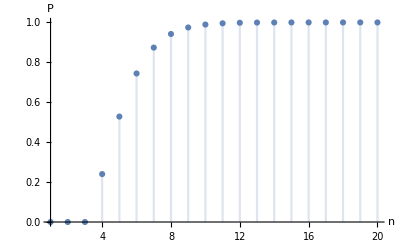

```mathematica
DiscretePlot[Probability[x ≥ 4, x \[Distributed] BinomialDistribution[n, 0.7]],{n,1,20},AxesLabel -> {n,P},LabelStyle ->Bold]
```

## 2η Άσκηση

Να αποδείξετε ότι η χαρακτηριστική συνάρτηση της εκθετικής κατανομής με παράμετρο λ είναι  φ(t)=λ/(λ-it) . Με τη βοήθεια της χαρακτηριστικής συνάρτησης να υπολογίσετε τις 4 πρώτες ροπές της εκθετικής κατανομής.

Λύση

```mathematica
f = λ Exp[- λ*x]
```

ⅇ^(-x λ) λ

```mathematica
ϕ = Integrate[Exp[I*t*x]*f,{x,0,Infinity}]
```

ConditionalExpression[λ/(-ⅈ t+λ), Im[t]+Re[λ]>0]

```mathematica
ϕ1= λ/(- I *t + λ)
```

λ/(-ⅈ t+λ)

Έχοντας βρει την φ, τώρα θα βρούμε και τις ροπές:

Ροπή 1ης τάξης

```mathematica
μ1 = D[ϕ1,{t,1}]/I /.t->0
```

1/λ

Ροπή 2ης τάξης

```mathematica
μ2 = D[ϕ1,{t,2}]/I^2/.t->0
```

2/λ^2

Ροπή 3ης τάξης

```mathematica
μ3 = D[ϕ1,{t,3}]/I^3/.t->0
```

6/λ^3

Ροπή 4ης τάξης

```mathematica
μ4 = D[ϕ1,{t,4}]/I^4/.t->0
```

24/λ^4

## 3η Άσκηση

Έστω η συνεχής τυχαία μεταβλητή X, x ∈ [0, +∞) η οποία ακολουθεί την κατανομή Weibull με πυκνότητα πιθανότητας f (x; k, λ) =  k/λ (x /λ)^(k−1) e^(−(x/λ)^k), για k = 2, λ = 1.

Να παράξετε ένα τυχαίο δείγμα Σ από 1000 τιμές της τυχαίας μεταβλητής.

Από το τυχαίο δείγμα Σ να υπολογίσετε τις 4 πρώτες ροπές της κατανομής.

Χρησιμοποιώντας τις ροπές του ερωτήματος b, να γράψετε μία προσέγγιση ϕ̂(t) της χαρακτηριστικής συνάρτησης της κατανομής και από αυτή να εξάγετε μια προσέγγιση f (̂ x) της πυκνότητας πιθανότητας.

Να παραστήσετε την πυκνότητα πιθανότητας του Σ υπό τη μορφή ιστογράμματος και να ζωγραφίσετε στο ίδιο διάγραμμα τις f (̂ x) και f (x).

Λύση

Να παράξετε ένα τυχαίο δείγμα Σ από 1000 τιμές της τυχαίας μεταβλητής.

```mathematica
data = RandomVariate[WeibullDistribution[2,1],1000];
```

```mathematica
Weibull = PDF[WeibullDistribution[2, 1], x]
```

Piecewise[{{2 ⅇ^(-x^2) x, x>0}, {0, True}}]

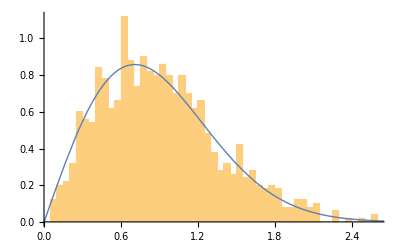

```mathematica
Show[
 Histogram[data, 50, "PDF"],
 Plot[PDF[WeibullDistribution[2, 1], x], {x, 0, 4}, 
  PlotStyle -> Thick]]
```

Υπολογισμός των 4 πρώτων ροπών

```mathematica
μ = Table[Mean[data^(i-1)],{i,1,4}]
```

{1.,0.906955,1.03534,1.38768}

Χρησιμοποιώντας τις ροπές του ερωτήματος b, προσεγγίζουμε το φ(t) της χαρακτηριστικής συνάρτησης της κατανομής

```mathematica
ϕ=Sum[Part[μ,j]*(I*t)^(j-1)/((j-1)!),{j,1,4}]
```

1.+(0.+0.906955 ⅈ) t-0.517668 t^2-(0.+0.231279 ⅈ) t^3

και τώρα βρίσκουμε την f(x)

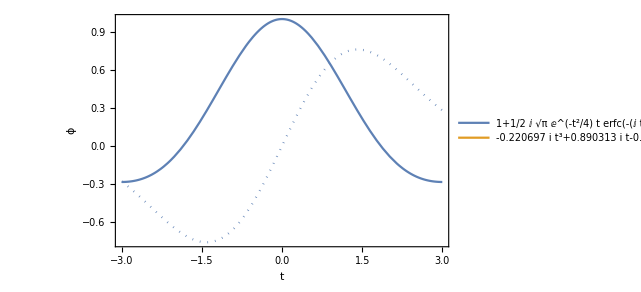

```mathematica
ReImPlot[{CharacteristicFunction[WeibullDistribution[2,1],t],ϕ},{t,-3,3},PlotLegends->Placed[{CharacteristicFunction[WeibullDistribution[2,1],t],1+i 0.890313t-0.501046 t^2-0.220697i t^3},Bottom],Frame->True,FrameLabel->{"t","ϕ"},LabelStyle->{FontFamily->"Times New Roman".20}]
```

## 4η Άσκηση

Θεωρήστε Ν ανεξάρτητα δείγματα της συνεχούς τυχαίας μεταβλητής που ακολουθεί την εκθετική κατανομή με λ = 2 και της Υ που ακολουθεί την ομοιόμορφη κατανομή στο διάστημα [0,4]. Να εκτελέσετε 10000 δοκιμές όπου επιλέγετε τυχαία Ν δείγματα από κάθε μεταβλητή και υπολογίζετε τις ποσότητες  x̄ = 1/N∑_(i=1)^N x_i και  ȳ =  1/N∑_(i=1)^N y_i. Να επαναλάβετε για Ν = 2, 20, 200 και να παραστήσετε τα ιστογράμματα των  x̄ και ȳ (κοινό διάγραμμα για όλες τις τιμές του N). Υπολογίστε σε κάθε περίπτωση την τυπική απόκλιση της κατανομής των x̄, ȳ και σχολιάστε το αποτέλεσμα.

Λύση

Δημιουργία δείγματος των Χ για Ν = 2, 20 και 200 και μετά πλοτάρουμε το ιστόγραμμα του x̄ για κάθε Ν.

```mathematica
ClearAll;
```

```mathematica
n = {2,20,200};
```

```mathematica
matΧ1 = Table[RandomVariate[ExponentialDistribution[2],n[[1]]],{i,1,10000}];
```

```mathematica
matΧ2 = Table[RandomVariate[ExponentialDistribution[2],n[[2]]],{i,1,10000}];
```

```mathematica
matΧ3 = Table[RandomVariate[ExponentialDistribution[2],n[[3]]],{i,1,10000}];
```

Τα σφάλματα έχουν ως εξής

```mathematica
SDX = {StandardDeviation[Mean[Transpose[matΧ1]]],StandardDeviation[Mean[Transpose[matΧ2]]],StandardDeviation[Mean[Transpose[matΧ3]]]}
```

{0.360048,0.110914,0.0354663}

```mathematica
SDX2 = {SDX[[1]]^2/2,SDX[[2]]^2/20,SDX[[3]]^2/200}
```

{0.0648174,0.000615094,6.28928×10^-6}

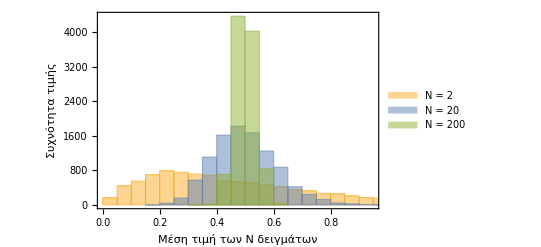

```mathematica
Histogram[{Mean[Transpose[matΧ1]],Mean[Transpose[matΧ2]],Mean[Transpose[matΧ3]]},50,ChartLegends -> Placed[{"N = 2", "N = 20",  "N = 200"}, Right],Frame->True,FrameLabel->{"Μέση τιμή των Ν δειγμάτων","Συχνότητα τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

Δημιουργία τώρα για τα Υ για Ν = 2, 20 και 200 και μετά πλοτάρουμε το ιστόγραμμα του ȳ για κάθε Ν.

```mathematica
matY1 = Table[RandomVariate[UniformDistribution[{0,4}],n[[1]]],{i,1,10000}];
matY2 = Table[RandomVariate[UniformDistribution[{0,4}],n[[2]]],{i,1,10000}];
matY3 = Table[RandomVariate[UniformDistribution[{0,4}],n[[3]]],{i,1,10000}];
```

Τα σφάλματα έχουν ως εξής

```mathematica
SDY= {StandardDeviation[Mean[Transpose[matY1]]],StandardDeviation[Mean[Transpose[matY2]]],StandardDeviation[Mean[Transpose[matY3]]]}
```

{0.824982,0.25892,0.0822416}

```mathematica
SDY2 = {SDY[[1]]^2/2,SDY[[2]]^2/20,SDY[[3]]^2/200}
```

{0.340298,0.00335197,0.0000338184}

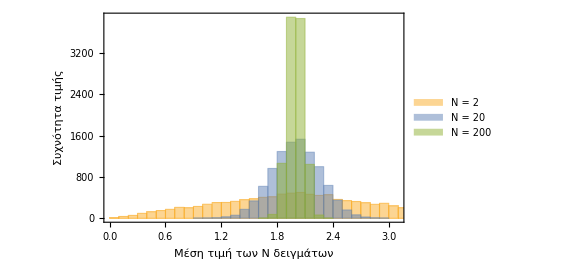

```mathematica
Histogram[{Mean[Transpose[matY1]],Mean[Transpose[matY2]] ,Mean[Transpose[matY3]]} ,50,ChartLegends -> Placed[{"N = 2", "N = 20",  "N = 200"}, Right],Frame->True,FrameLabel->{"Μέση τιμή των Ν δειγμάτων","Συχνότητα τιμής"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

## 5η Άσκηση

Να υπολογίσετε με τη μέθοδο  Monte Carlo το ολοκλήρωμα I =  ∫_Ω ∫ x^3 y dxdy, όπου Ω είναι το χωρίο του επιπέδου x-y όπου x^2 + y^2 ⩽ 4, x,y ≥ 0. (Υπόδειξη: τα ζεύγη x,y στο χωρίο Ω μπορούν να παραχθούν σε πολικές συντεταγμένες). Χρησιμοποιήστε Ν=5, 50, 200, 500 σημεία και επαναλάβετε 10000 φορές για κάθε τιμή του Ν. Να παραστήσετε γραφικά τις κατανομές (ιστογράμματα) των 10000 δοκιμών της ποσότητας I_Ν και να υπολογίσετε τις αντίστοιχες μέσες τιμές μ_Ν = E[I_Ν] και τις τυπικές αποκλίσεις σ_Ν = √Var[I_N]. Τέλος να παραστήσετε γραφικά τα μ_Ν συναρτήσει του N ως σημεία με σφάλμα σ_Ν. Στο ίδιο διάγραμμα να ζωγραφίσετε και την ευθεία που αντιστοιχεί στην αναλυτική τιμή του ολοκληρώματος (μπορείτε να χρησιμοποιήσετε τον σύνδεσμο https://www.symbolab.com/solver/double-integrals-calculator. Σχολιάστε το αποτέλεσμα. Επίσης να ζωγραφίσετε την ποσότητα σ_Ν/μ_Ν συναρτήσει του Ν. Πόσα σημεία Ν απαιτούνται (κατά προσέγγιση) για να επιτύχουμε τυπική απόκλιση μικρότερη του 1% της μέσης τιμής?

Λύση

```mathematica
Ireal =Integrate[x^3y Boole[x^2 + y^2 ≤ 4 ], {x, 0, Infinity}, {y, 0, Infinity}]//N
```

2.66667

Περιοχή ενδιαφέροντος για τον υπολογισμό του ολοκληρώματος

```mathematica
reg=ImplicitRegion[{x^2+y^2 ≤ 4 ,y≥0,x≥0},{x,y}]
```

Ορισμός της συνάρτησης

```mathematica
f[x_,y_]:=x^3 y
```

Εμβαδόν της περιοχής

```mathematica
Subscript[V, d]=Area[reg]
```

Δημιουργία 10.000 τυχαίων σημείων

```mathematica
g[]:=Block[{t,r},
t=RandomVariate[UniformDistribution[{0,π/2}]] ;
r=Sqrt[RandomVariate[UniformDistribution[{0,4}]]];
{r Cos[t],r Sin[t]}]
ListPlot[Table[g[],{10000}],AspectRatio->Automatic,PlotRange->{{-2,2},{-2,2}}]
```

Υπολογισμός του ολοκληρώματος για 5 σημεία (για 10.000 φορές)

```mathematica
I5=ParallelTable[n=Table[g[],{5}]ᵀ;Subscript[V, d]/5 Total[f[n[[1]],n[[2]]]],{10000}];
```

Υπολογισμός του ολοκληρώματος για 50 σημεία (για 10.000 φορές)

```mathematica
I50=ParallelTable[n=Table[g[],{50}]ᵀ;Subscript[V, d]/50 Total[f[n[[1]],n[[2]]]],{10000}];
```

Υπολογισμός του ολοκληρώματος για 200 σημεία (για 10.000 φορές)

```mathematica
I200=ParallelTable[n=Table[g[],{200}]ᵀ;Subscript[V, d]/200 Total[f[n[[1]],n[[2]]]],{10000}];
```

Υπολογισμός του ολοκληρώματος για 500 σημεία (για 10.000 φορές)

```mathematica
I500=ParallelTable[n=Table[g[],{500}]ᵀ;Subscript[V, d]/500 Total[f[n[[1]],n[[2]]]],{10000}];
```

Μέσες τιμές και τυπικές αποκλίσεις

```mathematica
μΙ5=Mean[I5]
```

```mathematica
σΙ5=StandardDeviation[I5]
```

```mathematica
μΙ50=Mean[I50]
```

```mathematica
σΙ50=StandardDeviation[I50]
```

```mathematica
μΙ200=Mean[I200]
```

```mathematica
σΙ200=StandardDeviation[I200]
```

```mathematica
μΙ500=Mean[I500]
```

```mathematica
σΙ500=StandardDeviation[I500]
```

Ιστογράμματα

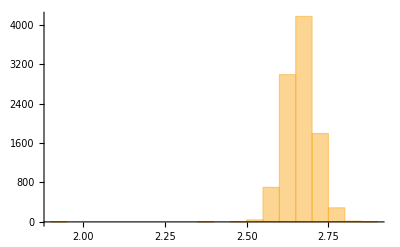

```mathematica
Histogram[I5]
```

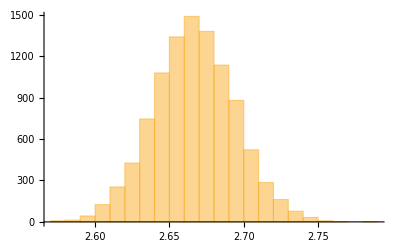

```mathematica
Histogram[I50]
```

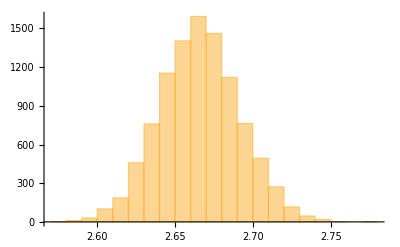

```mathematica
Histogram[I200]
```

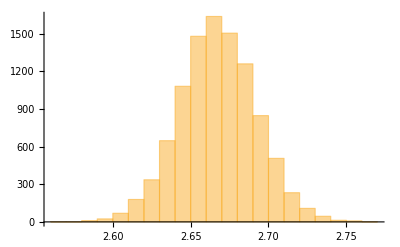

```mathematica
Histogram[I500]
```

Γράφικη παράσταση της μέσης τιμής για κάθε Ν με τα αντίστοιχα σφάλματα και η αναλυτική τιμή του ολοκληρώματος.

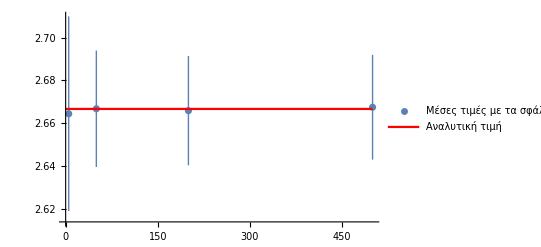

```mathematica
L1=ListPlot[{{{5,PlusMinus[μΙ5,σΙ5]} ,{50,PlusMinus[μΙ50,σΙ50]}, {200,PlusMinus[μΙ200,σΙ200]},{500,PlusMinus[μΙ500,σΙ500]}}}, PlotRange->All,PlotLegends ->{"Μέσες τιμές με τα σφάλματα τους"}];
P1=Plot[y = Ireal,{y,0,500},PlotStyle ->Red, PlotLegends->{"Αναλυτική τιμή"}];
Show[L1,P1]
```

```mathematica
vardata= {{5,σΙ5},{50,σΙ50}, {200,σΙ200},{500,σΙ500}}
```

{{5,0.04558},{50,0.0272628},{200,0.025605},{500,0.0245465}}

```mathematica
varpermeandata= {{5,σΙ5/μΙ5},{50,σΙ50/μΙ50}, {200,σΙ200/μΙ200},{500,σΙ500/μΙ500}}
```

```mathematica
fittedFunction=LinearModelFit[Log[varpermeandata],x,x]["Function"];
root ={x}/.FindRoot[{fittedFunction[x]==Log[0.01]},{x,8}];
newN=Round[E^(root[[1]])]
Inew=ParallelTable[n=RandomPoint[reg,newN]ᵀ;Subscript[V, d]/newN Total[f[n[[1]],n[[2]]]],{10000}];
```

219600

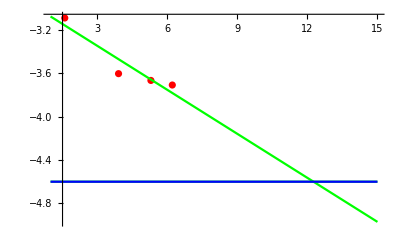

```mathematica
Show[ListPlot[Log[vardata],PlotStyle->Red],Plot[{fittedFunction[x],-4.6},{x,1,15},PlotStyle->Green],Plot[{-4.6},{x,1,15}, PlotStyle->Blue],PlotRange->All]
```

```mathematica
root
```

{12.2996}

```mathematica
newN
```

219600

```mathematica
StandardDeviation[Inew]/Mean[Inew]
```

{0.0105034}

## 6η Άσκηση

Έστω οι τυχαίες μεταβλητές X,Y που ακολουθούν διδιάστατη κανονική κατανομή f(x,y) με μέσες τιμές (2,1), τυπικές αποκλίσεις (1, 4) και συντελεστή συσχέτισης  ρ = + 0.5. Να παράξετε ένα σύνολο 1000 (ψευδο)τυχαίων ζευγών (x,y) από την κατανομή αυτή χρησιμοποιώντας τον αλγόριθμο  Metropolis-Hastings και να το αποτυπώσετε σε ένα διάγραμμα x-y (scatter plot). Επιβεβαιώστε ότι οι μέσες τιμές και ο πίνακας διασποράς του δείγματος που παράξατε είναι συμβατά με τη θεωρητική κατανομή. Χρησιμοποιήστε κανονική συνάρτηση μεταφοράς T(x_(m+1)|x_m)=1/(√(2π)σ)exp[-1/(2 σ^2)(x_(m+1)-x_m)^2]  με παράμετρο σ της επιλογής σας. Να παράξετε τα διαγράμματα αυτοσυσχέτισης για διάφορες τιμές του σ και να τα συγκρίνετε μεταξύ τους. Αξιολογήστε τον αριθμό των αρχικών δειγμάτων που πρέπει να “πετάξετε” καθώς και τον αριθμό των δειγμάτων που πρέπει να “παρακάμψετε” μέχρι να χαθεί η αυτοσυσχέτιση σε κάθε περίπτωση.

Λύση

Δεδομένα άσκησης:

```mathematica
σx = 1;

σy = 4;

ρ = +0.5;
```

Θα τρέξουμε το κώδικα για 500.000 δείγματα

```mathematica
n=500000;
```

Η Function του αλγορίθμου

```mathematica
mcmcfun = Function[s,
   Module[{xm, ym, proposal, xp, yp, p2, p1, proposalSigma1 = σx, proposalSigma2 = σy,
     pdf = 1/((2*Pi) σx*σy Sqrt[1 - ρ^2])  Exp[-(1/( 2 (1 - ρ^2))) ((x^2/(σx^2)) + (   y^2/(σy^2)) - ((2 x*y*ρ)/(σx*σy)))]},
    {xm, ym} = s;
    xp = RandomReal[NormalDistribution[xm, proposalSigma1]];
    yp = RandomReal[NormalDistribution[ym, proposalSigma2]];
    p2 = pdf /. {x -> xp, y -> yp};
    p1 = pdf /. {x -> xm, y -> ym};
    proposal = p2/p1;
    If[RandomReal[{0,1}] ≤ proposal
     , {xp, yp}
     , {xm, ym}]]];
```

Δημιουργία 500.000 σημείων με αρχικό σημείο το (1,2) και τυπικές αποκλίσεις τις proposalSigma1 και proposalSigma2

```mathematica
(sim = NestList[
     mcmcfun[#] &, 
     {1,2}, 
     n-1];) // AbsoluteTiming
```

{42.2974,Null}

Πλοτάρουμε την αυτοσυσχέτιση R(k) με βήματα MCsteps

```mathematica
MCsteps=100;
Rx[k_]:=Sum[(Part[sim[[t]],2] - xmean)(Part[sim[[t+k]],2]- xmean),{t,1,n-k}]/Sum[(Part[sim[[t]],2] - xmean)^2,{t,1,n-k}]
Ry[k_]:=Sum[(Part[sim[[t]],2] - ymean)(Part[sim[[t+k]],2]- ymean),{t,1,n-k}]/Sum[(Part[sim[[t]],2] -ymean)^2,{t,1,n-k}]
ax = ParallelTable[Rx[x], {x, 0, MCsteps}];
ay = ParallelTable[Ry[x], {x, 0, MCsteps}];
```

Κάνουμε fit στις καμπύλες R(k) των X και Υ.

```mathematica
model=R0 Exp[-k/km ];
fit1=FindFit[ax,model,{R0,km},k]
```

{R0→1.13426,km→6.43032}

```mathematica
fit2=FindFit[ay,model,{R0,km},k]
```

{R0→1.13427,km→6.43027}

Το γράφημα αυτοσυσχέτισης

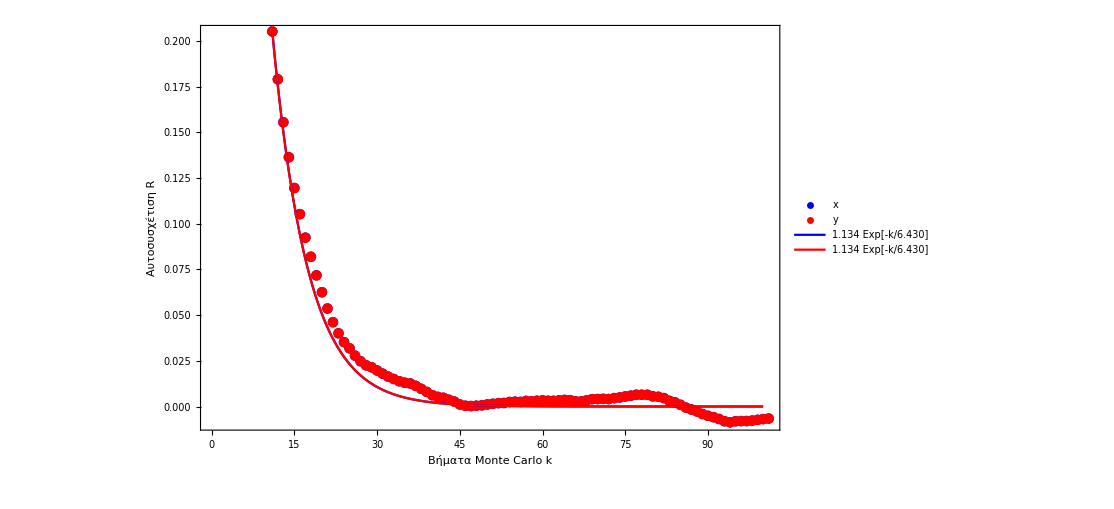

```mathematica
Show[
ListPlot[ax,PlotLegends->{"x"},PlotStyle->Blue],
ListPlot[ay,PlotLegends->{"y"},PlotStyle->Red],
Plot[1.1342647593678978 Exp[-k/6.430324672815287],{k,-10,100},PlotLegends->{"1.134 Exp[-k/6.430]"},PlotStyle->Blue],Plot[1.1342683655199424 Exp[-k/6.430267994116888],{k,-10,100},PlotLegends->{"1.134 Exp[-k/6.430]"},PlotStyle->Red],Frame->True,FrameLabel->{"Βήματα Monte Carlo k","Αυτοσυσχέτιση R"},LabelStyle->{FontFamily->"Times New Roman",20}]
```

Πετάμε τα μισά πρώτα σημεία

```mathematica
simhalf=Drop[sim,250000];
```

Και διαλέγουμε 1000 τυχαία από τα υπόλοιπα, για να έχει χαθεί σίγουρα η αυτοσυσχέτιση

```mathematica
sim3=RandomChoice[simhalf,1000];
```

Το scatter plot των 1000 σημείων

```mathematica
ListPlot[sim3,Frame->True,FrameLabel->{x,y},LabelStyle->{FontFamily->"Times New Roman",20}]
```

Ο πίνακας συνδιασποράς

```mathematica
Covariance[sim3]//MatrixForm
```

(1.04011 | 1.8295
1.8295 | 15.3822)

Οι μέσες τιμές και οι τυπικές αποκλίσεις

```mathematica
Mean[sim3]
```

{-0.00656646,-0.203662}

```mathematica
StandardDeviation[sim3]
```

{1.01986,3.92202}